```mathematica
$Assumptions={x<1/3,σ∈Reals,ϵ>0,A>0,r>0};
```

```mathematica
f[x_]=-1/3 Log[1-3x];
```

```mathematica
fs[σ_]=Integrate[f[x] E^(-I x (σ+I ϵ)),{x,-∞,1/3}]/.{ϵ->0}
```

(ⅈ ⅇ^(-(ⅈ σ)/3) (EulerGamma+Log[-(ⅈ σ)/3]))/(3 σ)

```mathematica
ContourPlot[Re[fs[Reσ+I Imσ]],{Reσ,-1,1},{Imσ,-1,1},PlotLegends->Automatic]
```

-Graphics-

```mathematica
ContourPlot[Im[fs[Reσ+I Imσ]],{Reσ,-1,1},{Imσ,-1,1},PlotLegends->Automatic]
```

-Graphics-

```mathematica
Nm=Integrate[1/Sqrt[2π A] E^(-x^2/(2A)),{x,-∞,1/3}]
```

1/2 (1+Erf[1/(3 √2 √A)])

```mathematica
Kn[σ_]=Integrate[1/(Sqrt[2π A]Nm)E^(-x^2/(2A))E^(-I x σ),{x,-∞,1/3}]
```

(ⅇ^(-(A σ^2)/2) (1+Erf[(1+3 ⅈ A σ)/(3 √2 √A)]))/(1+Erf[1/(3 √2 √A)])

```mathematica
meanf[A_]=Integrate[f[x] 1/(Sqrt[2π A]Nm)E^(-x^2/(2A)),{x,-∞,1/3}]//Simplify
```

1/(54 A √(2 π) (1+Erf[1/(3 √2 √A)]))(-12 √A HypergeometricPFQ[{1/2,1/2},{3/2,3/2},-1/(18 A)]+√π (-√2 HypergeometricPFQ[{1,1},{3/2,2},-1/(18 A)]+9 √2 A (EulerGamma+Log[2/(9 A)]+Erf[1/(3 √2 √A)] (2 EulerGamma+Log[2/(9 A)]))-3 √A Hypergeometric1F1Regularized^(0,1,0)[1/2,3/2,-1/(18 A)]))

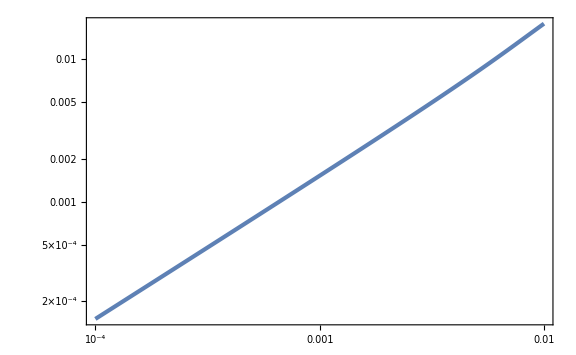

```mathematica
LogLogPlot[meanf[A],{A,10^-4,10^-2}]
```

```mathematica
C2[A_,r_]=A{{1,Sin[r]/r},{Sin[r]/r,1}};
```

```mathematica
P2[x1_,x2_,r_,A_]=1/(2π Sqrt[Det[C2[A,r]]])Exp[-1/2({{x1,x2}}.Inverse[C2[A,r]].{{x1},{x2}})[[1,1]]]//Simplify
```

(ⅇ^(-(r (r (x1^2+x2^2)-2 x1 x2 Sin[r]))/(A (-1+2 r^2+Cos[2 r]))))/(2 A π √(1-Sin[r]^2/r^2))

```mathematica
Integrate[P2[x1,x2,r,A],{x1,-∞,∞},{x2,-∞,∞}]
```

ConditionalExpression[1, A (2 r^2+Cos[2 r])>A]

```mathematica
Integrate[Exp[-1/2({{s1,s2}}.C2[A,r].{{s1},{s2}})[[1,1]]] E^(-I k r cos)2π r^2,{r,0,∞},{cos,-1,1}]
```

$Aborted

```mathematica
fs[σ]/(2π)Kn[σ]//Simplify
```

(ⅈ ⅇ^(-1/6 σ (2 ⅈ+3 A σ)) (1+Erf[(1+3 ⅈ A σ)/(3 √2 √A)]) (EulerGamma+Log[-(ⅈ σ)/3]))/(6 π σ (1+Erf[1/(3 √2 √A)]))

```mathematica
Series[fs[σ]/(2π)Kn[σ],{σ,0,0}]//Simplify
```

(ⅈ (2 EulerGamma-ⅈ π-2 Log[3]+2 Log[σ]))/(12 π σ)+(ⅇ^(-1/18/A) (ⅇ^(1/18/A)-3 √A √(2/π)+ⅇ^(1/18/A) Erf[1/(3 √2 √A)]) (2 EulerGamma-ⅈ π-Log[9]+2 Log[σ]))/(36 π (1+Erf[1/(3 √2 √A)]))+O[σ]^1

```mathematica
Series[fs[I Imσ]/(2π)Kn[I Imσ]//Simplify,{Imσ,∞,0}]
```

ⅇ^((2 Imσ)/3-1/(18 A)+O[1/Imσ]^2) O[1/Imσ]^2

```mathematica
Series[fs[I Imσ]/(2π)Kn[I Imσ]//Simplify,{Imσ,-∞,0}]
```

ⅇ^((A Imσ^2)/2+Imσ/3+O[1/Imσ]^2) O[1/Imσ]^1+ⅇ^((2 Imσ)/3-1/(18 A)+O[1/Imσ]^2) O[1/Imσ]^2

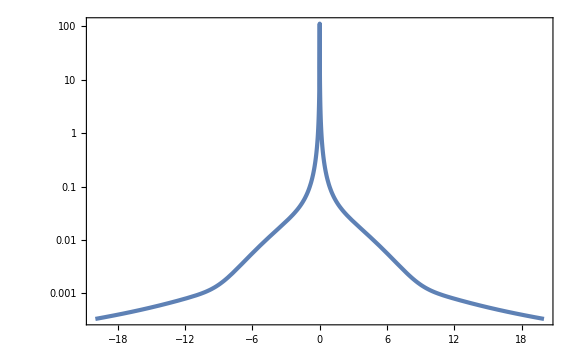

```mathematica
LogPlot[Abs[fs[σ]/(2π)Kn[σ]/.{A->0.1}],{σ,-20,20}]
```

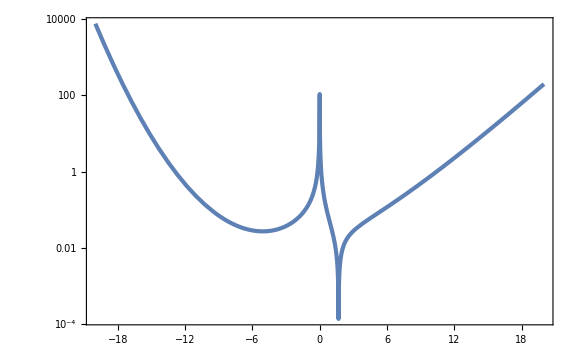

```mathematica
LogPlot[Abs[fs[I Imσ]/(2π)Kn[I Imσ]/.{A->0.1}],{Imσ,-20,20}]
```

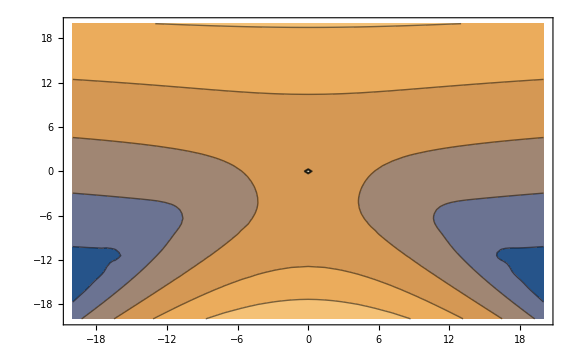

```mathematica
ContourPlot[Log[Abs[fs[Reσ+I Imσ]/(2π)Kn[Reσ+I Imσ]/.{A->0.1}]],{Reσ,-20,20},{Imσ,-20,20}]
```

```mathematica
Integrate[fs[σ]/(2π)Kn[σ],{σ,-∞,∞}]
```

Integrate::idiv: Integral of (ⅈ ⅇ^(-1/6 σ (2 ⅈ+3 A σ)) (1+Erf[(1+3 ⅈ A σ)/(3 √2 √A)]) (EulerGamma+Log[-(ⅈ σ)/3]))/(6 π σ (1+Erf[1/(3 √2 √A)])) does not converge on {-∞,∞}.

∫_(-∞)^∞ (ⅈ ⅇ^(-(ⅈ σ)/3-(A σ^2)/2) (1+Erf[(1+3 ⅈ A σ)/(3 √2 √A)]) (EulerGamma+Log[-(ⅈ σ)/3]))/(6 π σ (1+Erf[1/(3 √2 √A)]))ⅆσ